```mathematica
dh[r_] = D[r^2  / (r^2 + 1),r];
```

```mathematica
f[r_] = r * dh[Abs[r]]
```

r (-(2 Abs[r]^3)/((1+Abs[r]^2)^2)+(2 Abs[r])/(1+Abs[r]^2))

```mathematica
fw[ω_] = 2 Pi I / ω FourierTransform[f[t],t,ω]
```

-√2 π MeijerG[{{-1},{}},{{0,0},{-1/2}},ω^2/4]

```mathematica
L=20
```

20

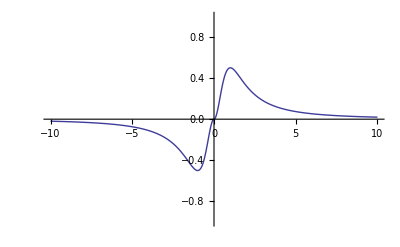

```mathematica
Plot[f[r],{r,-L/2,L/2},PlotRange-> {-1,1}]
```

```mathematica
fwTable = Table[fw[k],{k,-L/2,L/2,20/200}]//N;
```

Power::infy: Infinite expression 1/0. encountered.

```mathematica
ortsraum=Table[f[r],{r,-L/2,L/2, 20/200}]//N;
```

```mathematica
ortsraum[[1]] = 0;
ortsraum[[-1]] = 0;
```

```mathematica
impulsraum=Fourier[ortsraum];
```

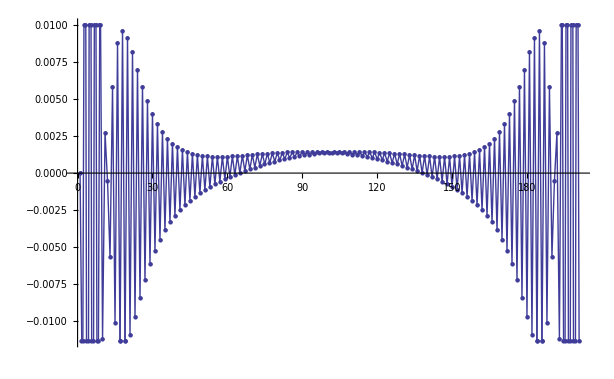

```mathematica
ListLinePlot[impulsraum//Re, PlotMarkers->{Automatic, 6}, ImageSize->Medium]
```

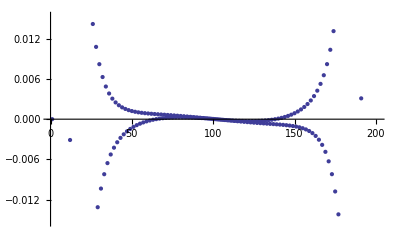

```mathematica
ListPlot[impulsraum//Im]
```

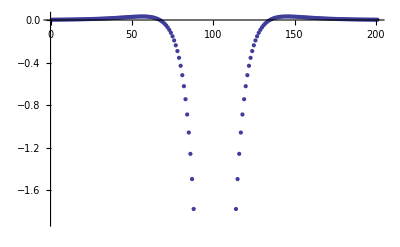

```mathematica
ListPlot[fwTable]
```